## Generate Voronoy foam

```mathematica
numGrains=30;
```

```mathematica
xBound=1;
yBound=3xBound;
```

```mathematica
pts=RandomPoint[Disk[{0,0},Max[{xBound,yBound}]],numGrains];
```

```mathematica
boundary = {{-xBound,xBound},{-yBound,yBound}};
```

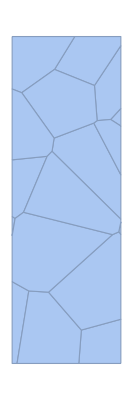

```mathematica
vMesh=VoronoiMesh[pts,boundary]
```

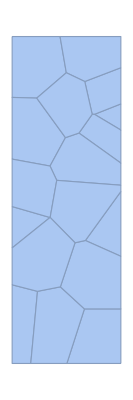
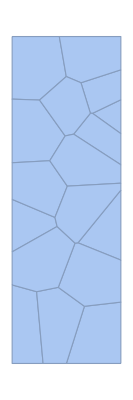
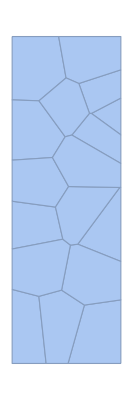
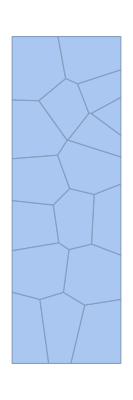
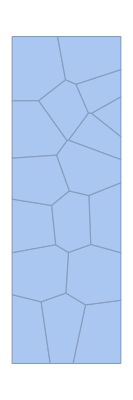
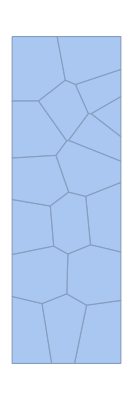
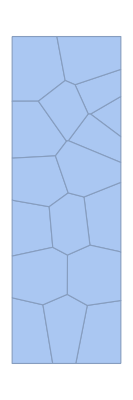
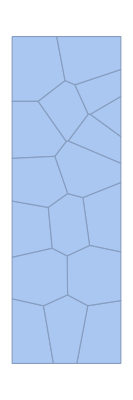
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vml=NestList[VoronoiMesh[Mean@@@MeshPrimitives[#,2],boundary]&,vMesh,10]
```

```mathematica
finalMesh=Last@vml;
```

```mathematica
grains=MeshPrimitives[finalMesh,2];
```

```mathematica
meshCentroids=Map[RegionCentroid,grains];
```

```mathematica
diameters=2*Abs[MapThread[SignedRegionDistance,{grains,meshCentroids}]];
```

```mathematica
averageGrainSize=Mean@diameters
```

0.699042

```mathematica
grainsCoord=Flatten[Union[Table[Cases[grains[[i]],Repeated[_,10]],{i,Length[grains]}]],1];
```

```mathematica
numGrains=Length@grainsCoord
```

17

### Commented out

```mathematica
(*nodes=Flatten[Cases[#,{_,_}]&/@MeshPrimitives[finalMesh,0],1];*)
```

```mathematica
(*Length[nodes]*)
```

```mathematica
(*edges=Flatten[Cases[#,{_,_}]&/@MeshPrimitives[finalMesh,1],1];*)
```

```mathematica
(*Length[edges]*)
```

```mathematica
(*assoc=Association[Table[nodes[[i]]->i,{i,Length[nodes]}]];*)
```

```mathematica
(*edges/.Normal[assoc];*)
```

```mathematica
(*<<NDSolve`FEM`*)
```

```mathematica
(*bmesh=ToBoundaryMesh["Coordinates"->nodes,"BoundaryElements"->{LineElement[edges/.Normal[assoc]]}]*)
```

```mathematica
(*RegionBounds[finalMesh]*)
```

```mathematica
(*Show[bmesh["Wireframe"]]*)
```

```mathematica
(*mesh=ToElementMesh[bmesh,"MeshOrder"->1,"MeshElementConstraint"->30,MaxCellMeasure->{"Length"->.15}]*)
```

```mathematica
(*Show[mesh["Wireframe"],Graphics[{EdgeForm[{Red,Thick}],Opacity[0.5],LightGray,grains}]]*)
```

```mathematica
(*mesh["Properties"]*)
```

```mathematica
(*meshTRIAcoord=mesh["Coordinates"];*)
```

```mathematica
(*numNode=Length@meshTRIAcoord*)
```

```mathematica
(*meshTRIAconnect=Join@@ElementIncidents[mesh["MeshElements"]];*)
```

```mathematica
(*numElements=Length@meshTRIAconnect*)
```

```mathematica
(*indexCenter[indexList_]:= Mean[meshTRIAcoord[[#]]&/@indexList]*)
```

## Generate mesh with a grain boundary layer

```mathematica
meshCentroids = Map[RegionCentroid, grains];
```

```mathematica
(*radii = Abs[MapThread[ SignedRegionDistance , {grains,meshCentroids}]];*)
```

```mathematica
scalePoints[points_,factor_]:=Module[{mean,newpoints,scalingMatrix},mean=Mean[points];
newpoints=(#-mean)&/@points;
scalingMatrix=ScalingMatrix[{factor,factor}];
newpoints=(scalingMatrix.#)&/@newpoints;
(#+mean)&/@newpoints]
```

```mathematica
thickFact=10;
thicknessGB = xBound/thickFact;
```

```mathematica
scalingFactor = (averageGrainSize - thicknessGB)/averageGrainSize
```

0.856947

```mathematica
scaledGrainCoord = MapThread[scalePoints,{grainsCoord,ConstantArray[scalingFactor,numGrains]}];
```

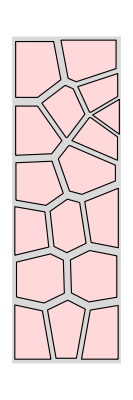

```mathematica
Graphics[{LightGray, Rectangle[{-xBound, -yBound}, {xBound, yBound}],
EdgeForm[Black],LightRed,Polygon /@ scaledGrainCoord}]
```

```mathematica
scaledNodeCoord=DeleteDuplicates[Flatten[scaledGrainCoord,1]];
```

```mathematica
Length[scaledNodeCoord]
```

85

```mathematica
assocSc=Association[Table[scaledNodeCoord[[i]]->i,{i,Length[scaledNodeCoord]}]];
```

```mathematica
grainsConnect=scaledGrainCoord/.Normal[assocSc];
```

### Make the nodes close to the boundary adhere to the boundary itself (if we don’t want to have a grain boundary that runs along the edges)

```mathematica
thrX=xBound-1.2thicknessGB;
thrY=yBound-1.2thicknessGB;
```

```mathematica
scaledNodeCoord = Map[{If[#[[1]]>thrX,xBound,#[[1]]],#[[2]]}&,scaledNodeCoord];
scaledNodeCoord=Map[{If[#[[1]]<-thrX,-xBound,#[[1]]],#[[2]]}&,scaledNodeCoord];
scaledNodeCoord=Map[{#[[1]],If[#[[2]]>thrY,yBound,#[[2]]]}&,scaledNodeCoord];
scaledNodeCoord=Map[{#[[1]],If[#[[2]]<-thrY,-yBound,#[[2]]]}&,scaledNodeCoord];
```

```mathematica
boundaryNodes=Select[scaledNodeCoord,Abs[#[[1]]]>thrX||Abs[#[[2]]]>thrY&];
```

### Viceversa if we want to have an edge running along the boundary

```mathematica
thrX=xBound-1.2thicknessGB;
thrY=yBound-1.2thicknessGB;
```

```mathematica
scaledNodeCoord = Map[{If[#[[1]]>thrX,xBound-thicknessGB,#[[1]]],#[[2]]}&,scaledNodeCoord];
scaledNodeCoord=Map[{If[#[[1]]<-thrX,-xBound+thicknessGB,#[[1]]],#[[2]]}&,scaledNodeCoord];
scaledNodeCoord=Map[{#[[1]],If[#[[2]]>thrY,yBound-thicknessGB,#[[2]]]}&,scaledNodeCoord];
scaledNodeCoord=Map[{#[[1]],If[#[[2]]<-thrY,-yBound+thicknessGB,#[[2]]]}&,scaledNodeCoord];
```

```mathematica
boundaryNodes=Select[scaledNodeCoord,Abs[#[[1]]]>thrX||Abs[#[[2]]]>thrY&];
```

### Continue from here

```mathematica
Clear[edgeNodes]
```

```mathematica
edgeList={};
```

```mathematica
collectEdges[edge:{begin_,end_}]:=
Block[{sortedEdge = Sort[edge],location},
 If[
!MemberQ[edgeList,sortedEdge],
AppendTo[edgeList,sortedEdge];
edgeNodes[Length[edgeList]]=sortedEdge;
edgeNodes[-Length[edgeList]]=Reverse[sortedEdge];

Return[Length[edgeList]],
location = Position[edgeList,sortedEdge][[1,1]];
If[edge == sortedEdge,Return[location],Return[-location]];
]
]
```

```mathematica
makeEdges[polygon_]:= Block[{edges},
edges =Transpose[{polygon,RotateRight[ polygon]}];
collectEdges/@edges
]
```

```mathematica
makeEdges/@grainsConnect;
```

```mathematica
edgeListExplic={};
```

```mathematica
For[i=1,i<=Total[Length[#]&/@grainsConnect],i++,AppendTo[edgeListExplic,edgeNodes[i]]]
```

```mathematica
sublist=Select[edgeListExplic,#[[2]]-#[[1]]>1&];
```

```mathematica
edgeListExplicPruned=Select[edgeListExplic,#[[2]]-#[[1]]==1&];
```

```mathematica
edgeListExplicComplete=Union[edgeListExplicPruned,RotateRight[#]&/@sublist];
```

```mathematica
allLineElements=Join[{{1,2},{2,3},{3,4},{4,1}},edgeListExplicComplete+4];
```

```mathematica
Join[{4},Length[#]&/@grainsConnect];
```

```mathematica
lineElements=FoldPairList[TakeDrop,allLineElements,Join[{4},Length[#]&/@grainsConnect]];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
lineElementList = LineElement[#]&/@lineElements;
```

```mathematica
allNodes=Join[{{-xBound,-yBound},{xBound,-yBound},{xBound,yBound},{-xBound,yBound}},scaledNodeCoord];
```

```mathematica
bmeshGB=ToBoundaryMesh["Coordinates"->allNodes,"BoundaryElements"->lineElementList];
```

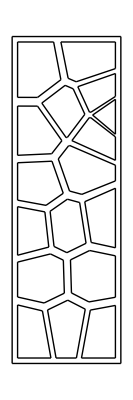

```mathematica
Show[bmeshGB["Wireframe"]]
```

```mathematica
meshGB=ToElementMesh[bmeshGB,"MeshOrder"->1,MeshQualityGoal->"Maximal","ImproveBoundaryPosition"->True]
```

ElementMesh[{{-1.,1.},{-3.,3.}},{TriangleElement[<1954>]}]

```mathematica
imageMesh=Show[
meshGB["Wireframe"],
meshGB["Wireframe"["MeshElement"->"BoundaryElements","MeshElementStyle"->{Red}]],ImageSize->Large];
```

```mathematica
Export[NotebookDirectory[]<>"Mesh_"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".eps",imageMesh]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/Mesh_230grains50.eps

```mathematica
meshTRIAcoordGB=meshGB["Coordinates"];
```

```mathematica
numNodeGB=Length@meshTRIAcoordGB
```

1036

```mathematica
meshTRIAconnectGB=Join@@ElementIncidents[meshGB["MeshElements"]];
```

```mathematica
numElementsGB=Length@meshTRIAconnectGB
```

1954

```mathematica
indexCenterGB[indexList_]:= Mean[meshTRIAcoordGB[[#]]&/@indexList]
```

```mathematica
Export[NotebookDirectory[]<>"TriaNodesPolycrystal2D_"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".csv",meshTRIAcoordGB]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/TriaNodesPolycrystal2D_230grains50.csv

```mathematica
Export[NotebookDirectory[]<>"TriaElementsPolycrystal2D_"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".csv",meshTRIAconnectGB]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/TriaElementsPolycrystal2D_230grains50.csv

## Convert the mesh: triangles to quadrilaterals

```mathematica
subsequence[1]={{1,2},{2,3},{3,1}}
```

{{1,2},{2,3},{3,1}}

```mathematica
subsequence[i_]:=(subsequence[i]=Module[{previousSequenceFirst=First[subsequence[i-1]][[1]],previousSequenceLast=Last[subsequence[i-1]][[1]]},{{previousSequenceLast+1,previousSequenceLast+2},{previousSequenceLast+2,previousSequenceLast+3},{previousSequenceLast+3,previousSequenceLast+1}}])

icount=1;
sequencesAt=NestList[(icount++;Join[#,subsequence[icount]])&,subsequence[1],numElementsGB];
```

```mathematica
edgesSequence=sequencesAt[[numElementsGB]];
```

```mathematica
edgesGB=Partition[Flatten[meshTRIAconnectGB][[Flatten[edgesSequence]]],2];
```

```mathematica
midpoints= Partition[indexCenterGB/@edgesGB,3];
```

```mathematica
elementCenters=indexCenterGB/@meshTRIAconnectGB;
```

```mathematica
elementNodesXYZ = meshTRIAconnectGB[[#]]&/@meshTRIAconnectGB;
```

```mathematica
quad1=ParallelTable[Polygon[{midpoints[[i,3]],meshTRIAconnectGB[[i,1]],midpoints[[i,1]],elementCenters[[i]]}],{i,1,numElementsGB}];
```

```mathematica
quad2=ParallelTable[Polygon[{midpoints[[i,1]],meshTRIAconnectGB[[i,2]],midpoints[[i,2]],elementCenters[[i]]}],{i,1,numElementsGB}];
```

```mathematica
quad3=ParallelTable[Polygon[{midpoints[[i,2]],meshTRIAconnectGB[[i,3]],midpoints[[i,3]],elementCenters[[i]]}],{i,1,numElementsGB}];
```

```mathematica
midpointsList=Flatten[midpoints,1];
```

```mathematica
newNodes = Join[midpointsList,elementCenters];
```

```mathematica
newNodesNumber=Max[Flatten[meshTRIAconnectGB]]+ Range[Length[midpointsList]+Length[elementCenters]];
```

```mathematica
newNodeRules = Thread[Rule[newNodes,newNodesNumber]];
```

```mathematica
quad1Incidence=ParallelTable[{midpoints[[i,3]]/.newNodeRules,meshTRIAconnectGB[[i,1]],midpoints[[i,1]]/.newNodeRules,elementCenters[[i]]/.newNodeRules},{i,1,numElementsGB}];
```

```mathematica
quad2Incidence=ParallelTable[{midpoints[[i,1]]/.newNodeRules,meshTRIAconnectGB[[i,2]],midpoints[[i,2]]/.newNodeRules,elementCenters[[i]]/.newNodeRules},{i,1,numElementsGB}];
```

```mathematica
quad3Incidence=ParallelTable[{midpoints[[i,2]]/.newNodeRules,meshTRIAconnectGB[[i,3]],midpoints[[i,3]]/.newNodeRules,elementCenters[[i]]/.newNodeRules},{i,1,numElementsGB}];
```

```mathematica
allNodes=Join[meshTRIAcoordGB,newNodes];
```

```mathematica
allNodesNumbered=Partition[Flatten[Riffle[Range[Length[allNodes]],allNodes]],3];
```

```mathematica
Dimensions[allNodesNumbered]
```

{8852,3}

```mathematica
quadElements=Join[quad1Incidence,quad2Incidence,quad3Incidence];
```

```mathematica
numQuadElem=Length@quadElements
```

5862

```mathematica
quadElementsNumbered=Partition[Flatten[Riffle[Range[Length[quadElements]],quadElements]],5];
```

```mathematica
Export[NotebookDirectory[]<>"nodesPolycrystal2D_"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".csv",allNodes]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/nodesPolycrystal2D_230grains50.csv

```mathematica
Export[NotebookDirectory[]<>"elementsPolycrystal2D_"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".csv",quadElements]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/elementsPolycrystal2D_230grains50.csv

## Assign a grain to each finite element (grains will be treated as material IDs)

```mathematica
quadElementCenters =Mean[#]&/@(allNodes[[#]]&/@quadElements);
```

```mathematica
Length[quadElementCenters]
```

5862

```mathematica
scaledGrainCoordList=Flatten[scaledGrainCoord,1];
```

```mathematica
scaledGrainCoordList = scaledNodeCoord;
```

```mathematica
(*scaledGrainCoordList=Map[{If[#[[1]]>thrX,xBound,#[[1]]],#[[2]]}&,scaledGrainCoordList];
scaledGrainCoordList=Map[{If[#[[1]]<-thrX,-xBound,#[[1]]],#[[2]]}&,scaledGrainCoordList];
scaledGrainCoordList=Map[{#[[1]],If[#[[2]]>thrY,yBound,#[[2]]]}&,scaledGrainCoordList];
scaledGrainCoordList=Map[{#[[1]],If[#[[2]]<-thrY,-yBound,#[[2]]]}&,scaledGrainCoordList];*)
```

```mathematica
scaledGrainCoord=FoldPairList[TakeDrop,scaledGrainCoordList,Length[#]&/@grainsConnect];
```

```mathematica
ℛ=Polygon[#]&/@scaledGrainCoord;
```

```mathematica
mf=RegionMember[#]&/@ℛ;
```

```mathematica
mf[[1]][elementCenters[[1]]]
```

False

```mathematica
elementsPosition=Table[Table[mf[[i]][quadElementCenters[[j]]],{i,1,numGrains}],{j,1,numQuadElem}];
```

```mathematica
Dimensions@elementsPosition
```

{5862,17}

```mathematica
testOnElemPosition=Table[Position[elementsPosition[[i]],True],{i,numQuadElem}];
```

```mathematica
Dimensions@testOnElemPosition
```

{5862}

```mathematica
testOnElemPosition=testOnElemPosition//.{x_List}:>x;
```

```mathematica
testOnElemPosition=Map[If[Length[#]>0,#,{numGrains+1}]&,testOnElemPosition];
```

```mathematica
elementsGrain=Table[allNodes[[#]]&/@( quadElements[[#]]&/@Flatten[Position[testOnElemPosition,i]]),{i,numGrains+1}];
```

```mathematica
(*coordelementsGrain=Table[allNodes[[#]]&/@elementsGrain[[i]],{i,numeGrains+1}]*)
```

```mathematica
colorList=Flatten[Table[ColorData[1,"ColorList"],20]];
```

```mathematica
colorList=Join[colorList[[1;;numGrains]],{White}];
```

```mathematica
Length[colorList]
```

18

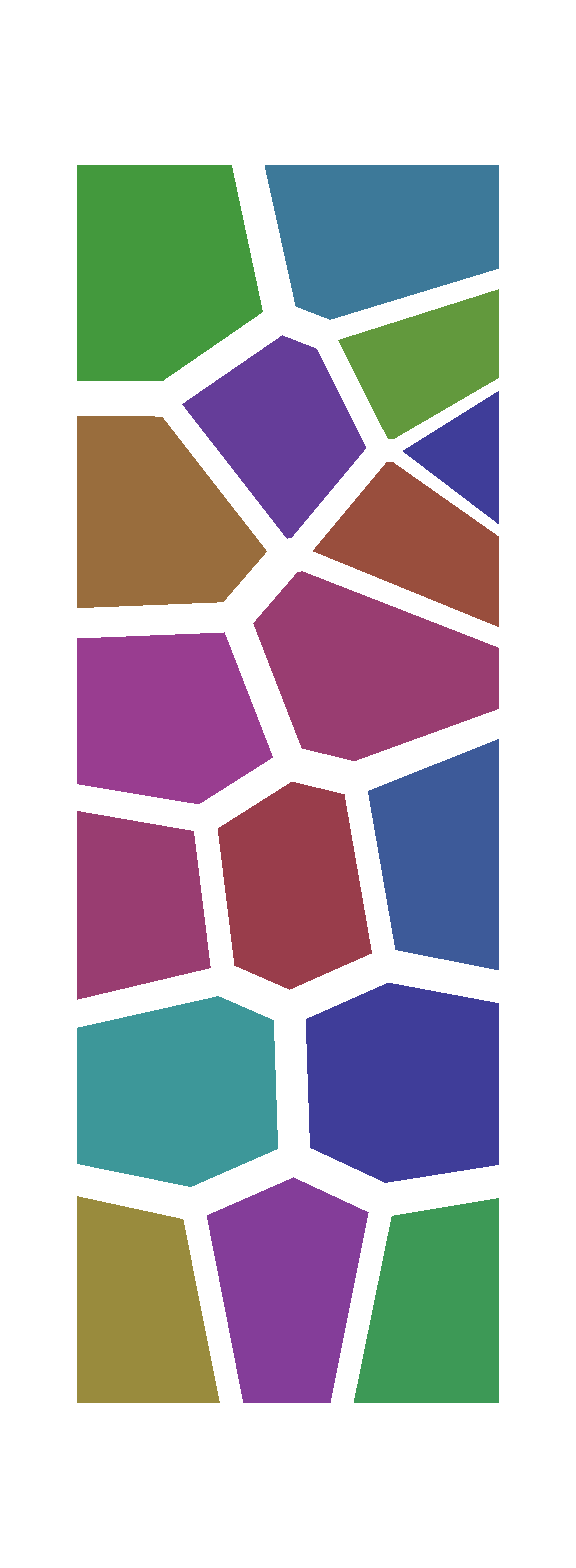

```mathematica
imageCryst=Show[Graphics[Table[{colorList[[i]],Polygon[#]&/@elementsGrain[[i]]},{i,numGrains+1}]],ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"GrainID"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".csv",testOnElemPosition-1]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/GrainID230grains50.csv

```mathematica
Export[NotebookDirectory[]<>"GrainID_image"<>ToString[ numGrains]<>"grains"<>ToString[thickFact]<>".pdf",imageCryst]
```

/Users/gio/Dropbox (MIT)/LI_Plating/polycrystal_Electrolyte/mesh_Generation/GrainID_image230grains50.pdf

### Assign a crystal orientation to each Voronoy mesh

```mathematica
(*firstCrystalDir=Table[{Cos[#],Sin[#]}&[RandomReal[{0,2Pi}]],{grains}]*)
```

```mathematica
(*secondCrystalDir=Cross[#]&/@firstCrystalDir*)
```

```mathematica
(*Graphics[{{Table[Arrow[{{0,0},firstCrystalDir[[i]]}],{i,5}]},{Red,Table[Arrow[{{0,0},secondCrystalDir[[i]]}],{i,5}]}}]*)
```

```mathematica
(*orthoNormVectors=Riffle[firstCrystalDir,secondCrystalDir];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"grainCrystalOrient.tsv",orthoNormVectors]*)
```